```mathematica
SetDirectory["L:/moose/trunk/wallaby/doc/tests/figures"];
fromMoose=Import["pressure_pulse.txt","Table"];
```

```mathematica
bulk=2*10^9;
visc = 0.001;
por = 0.1;
perm = 1*10^-15;
alpha = perm*bulk/visc/por;

p0=2*10^6;
pinf=3*10^6;
rho0=Exp[p0/bulk];
rhoinf=Exp[pinf/bulk];

rho[x_,t_] := rhoinf + (rho0-rhoinf)*Erf[x/Sqrt[4*alpha*t]];

p[x_,t_] := bulk*Log[rho[x,t]];
```

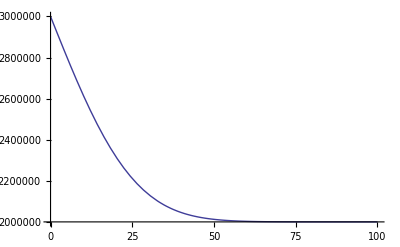

```mathematica
Plot[p[x,10000],{x,0,100}]
```

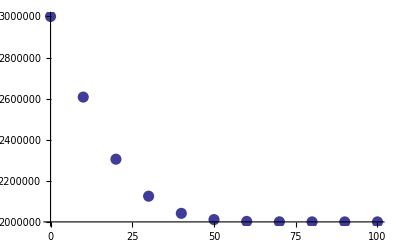

```mathematica
ListPlot[{#[[5]],#[[1]]}&/@fromMoose,PlotStyle->{PointSize[0.02]}]
```

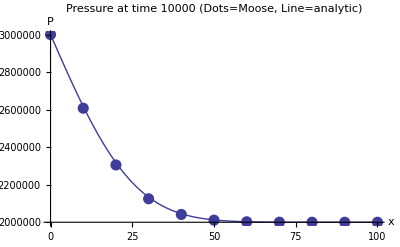

```mathematica
Show[%,%%,AxesLabel->{"x","P"},PlotLabel->"Pressure at time 10000 (Dots=Moose, Line=analytic)",PlotRange->All]
```

```mathematica
Export["pressure_pulse.eps",%,"EPS"]
```

pressure_pulse.eps